# Heun’s method for y’=x+y

```mathematica
data={{0,1}}; (*setting up a dataset to which the Do loop data will be sent to. includes initial condition y(0)=1*)
h=0.1; (*step size*)
y0=1;(*initial condition that will be used in the Do loop*)
```

```mathematica
Do[y1=y0+(((x-h)+y0)+(x+(y0+((x-h)+y0))*h))*h/2; AppendTo[data,{x,y1}]; y0=y1, {x,0.1,10,h}] (*calculating y(x+h)=y(x)+(y'(x)+y'(x+h))*h/2 with y'(x)=x+y and h=0.1 from x=0.1 to x=10 (x=0 is already included in the data set). for each iteration, the (x+h, y(x+h)) data is stored in the set "data" defined earlier.*)
```

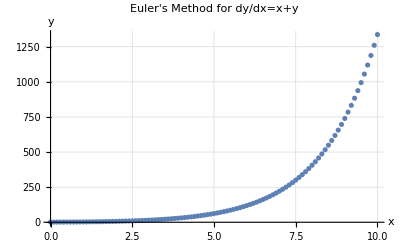

```mathematica
ListPlot[data,PlotLabel->"Heun's Method for dy/dx=x+y",GridLines->Automatic,AxesLabel->{"x","y"}](*plotting the data in the set "data", labeling the plot, setting up gridlines, and labeling the axes.*)
```

# Heun’s method for y’=ylny/x, N=10

```mathematica
data1={{2,Exp[1]}}; 
h2=0.2;
y2=Exp[1];
```

```mathematica
Do[y1=y2+(y2*Log[y2]/(x-h2)+(y2+y2*Log[y2]*h2/(x-h2))*Log[y2+y2*Log[y2]*h2/(x-h2)]/x)*h2/2; AppendTo[data1,{x,y1}]; y2=y1, {x,2.2,4,h2}]
```

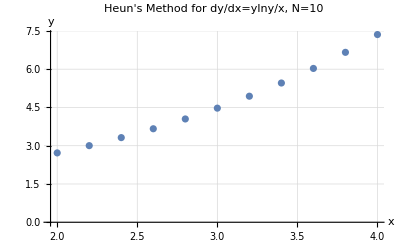

```mathematica
ListPlot[data1,PlotLabel->"Heun's Method for dy/dx=ylny/x, N=10",GridLines->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
solution=data1
```

{{2,ⅇ},{2.2,3.00306},{2.4,3.31763},{2.6,3.6651},{2.8,4.0489},{3.,4.47285},{3.2,4.94113},{3.4,5.45838},{3.6,6.02973},{3.8,6.66082},{4.,7.3579}}

# Heun’s method for y’=ylny/x, N=1000

```mathematica
data2={{2,Exp[1]}}; 
h3=0.002; 
y2=Exp[1];
```

```mathematica
Do[y1=y2+(y2*Log[y2]/(x-h3)+(y2+y2*Log[y2]*h3/(x-h3))*Log[y2+y2*Log[y2]*h3/(x-h3)]/x)*h3/2; AppendTo[data2,{x,y1}]; y2=y1, {x,2.002,4,h3}]
```

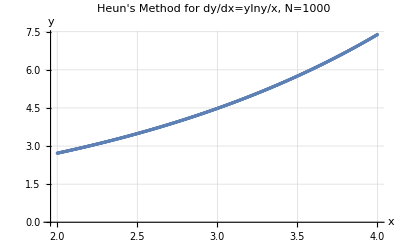

```mathematica
ListPlot[data2,PlotLabel->"Heun's Method for dy/dx=ylny/x, N=1000",GridLines->Automatic,AxesLabel->{"x","y"}]
```

# Heun' s method for y' = (x^2+y^2+1)^1/3, N = 10

```mathematica
data3={{0,0}}; 
h4=0.5;
y3=0;
```

```mathematica
Do[y1=y3+(((x-h4)^2+y3^2+1)^(1/3)+(x^2+(y3+((x-h4)^2+y3^2+1)^(1/3)*h4)^2+1)^(1/3))*h4/2; AppendTo[data3,{x,y1}]; y3=y1, {x,0.5,5,h4}]
```

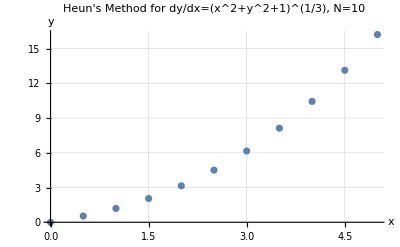

```mathematica
ListPlot[data3,PlotLabel->"Heun's Method for dy/dx=(x^2+y^2+1)^(1/3), N=10",GridLines->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
solution2=data3
```

{{0,0},{0.5,0.536179},{1.,1.19463},{1.5,2.05084},{2.,3.14415},{2.5,4.50338},{3.,6.15505},{3.5,8.12545},{4.,10.4411},{4.5,13.129},{5.,16.216}}

# Heun' s method for y' = (x^2 + y^2 + 1)^1/3, N = 1000

```mathematica
data4={{0,0}}; 
h5=0.005;
y3=0;
```

```mathematica
Do[y1=y3+(((x-h5)^2+y3^2+1)^(1/3)+(x^2+(y3+((x-h5)^2+y3^2+1)^(1/3)*h5)^2+1)^(1/3))*h5/2; AppendTo[data4,{x,y1}]; y3=y1, {x,0.005,5,h5}]
```

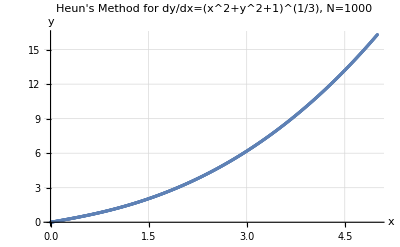

```mathematica
ListPlot[data4,PlotLabel->"Heun's Method for dy/dx=(x^2+y^2+1)^(1/3), N=1000",GridLines->Automatic,AxesLabel->{"x","y"}]
```